## Coil calculation for LG24B with experiment data for comparison

Authors: Mike Gehm <mgehm@phy.duke.edu>, Michael Stenner <mstenner@phy.duke.edu>, Zhichao Guo <guozc12@gmail.com>
Version: 2.0
Date: 2019.09.11

This Mathematica notebook calculates the magnetic field from sets of coils.  You must evaluate the "Definitions" section first.  See the "Description" section for help and examples.
This notebook was originally written by Mike Gehm and was modified by Michael Stenner.

This notebook was modified for LG24B lab in CUHK by Zhichao Guo.

## Constant and Global Function

### Global Function

```mathematica
ClearAll["Global`*"];
```

```mathematica
μ0=4 Pi* 10^-3;(* Gives answers in Gauss *)
```

```mathematica
Cons={
h->6.62606896*10^-34,
ℏ->h/(2π),
c->299792458,
α->e^2/(4π Subscript[ϵ, 0] ℏ c),
mp->1.67262174797*10^-27,
me->9.10938215*10^-31,
a0->(4π Subscript[ϵ, 0] ℏ^2)/(me e^2),
E0->(e^4 me)/(32 π^2 ℏ^2 Subscript[ϵ, 0]^2),
e->1.602176487*10^-19,
Subscript[ϵ, 0]->8.854187817*10^-12,
Subscript[μ, 0]->4π*10^-7,
μN->5.050783424*10^-27,
Subscript[μ, B]->9.27400915*10^-24,
Subscript[g, e]->2,
Z->1
};
```

## Definitions

#### Calculation Functions

These functions calculate the radial and axial field for a single coil.

```mathematica
Bz[r_,z_,coil_]:=
coil[[3]] * coil[[4]] *(μ0 /(2 Pi))/(√((coil[[1]] + r)^2+ (z-coil[[2]])^2)) * (EllipticK[(4 coil[[1]] r)/((coil[[1]]+r)^2+(z-coil[[2]])^2)] + ((coil[[1]]^2 - r^2 - (z-coil[[2]])^2)/((coil[[1]]-r)^2+(z-coil[[2]])^2))*EllipticE[(4 coil[[1]] r)/((coil[[1]]+r)^2+(z-coil[[2]])^2)]);
```

```mathematica
Br[r_,z_,coil_]:=
coil[[3]]*coil[[4]]* (z-coil[[2]])*(μ0 /(2 Pi r))/(√((coil[[1]] + r)^2+ (z-coil[[2]])^2))* (-EllipticK[(4 coil[[1]] r)/((coil[[1]]+r)^2+(z-coil[[2]])^2)] + ((coil[[1]]^2 + r^2 + (z-coil[[2]])^2)/((coil[[1]]-r)^2+(z-coil[[2]])^2))*EllipticE[(4 coil[[1]] r)/((coil[[1]]+r)^2+(z-coil[[2]])^2)]);
```

These functions calculate the field for all of the coils listed in "coils".

```mathematica
AxialField[r_,z_,coils_]:=
Module[{},
TempFunc[coil_]:=Bz[r,z,coil];
Plus@@Map[TempFunc,coils,{1}]
]
```

```mathematica
RadialField[r_,z_,coils_]:=
Module[{},
TempFunc[coil_]:=Br[r,z,coil];
Plus@@Map[TempFunc,coils,{1}]
]
```

This function calculates the field magnitude at any point using the previous functions.

```mathematica
FieldMag[r_,z_,coils_]:=
If[r==0,
AxialField[r,z,coils],
√(AxialField[r,z,coils]^2+RadialField[r,z,coils]^2)
];
```

#### Tools for generating "coils" list

```mathematica
WithTurns[precoil_,turns_]:=
Module[{},
TempFunc[coil_]:=Append[coil,turns];
Map[TempFunc,precoil,{1}]
]
```

```mathematica
WithCurrent[precoil_,current_]:=
Module[{},
TempFunc[coil_]:=Append[coil,current];
Map[TempFunc,precoil,{1}]
]
```

```mathematica
WithTurnsAndCurrent[precoil_,turns_,current_]:=
WithCurrent[WithTurns[precoil,turns],current]
```

```mathematica
Helmholtz[r_,z_,turns_,current_]:={{r,-z,turns,current},{r,z,turns,current}}
AntiHelmholtz[r_,z_,turns_,current_]:={{r,-z,turns,-current},{r,z,turns,current}}
TrueHelmholtz[z_,turns_,current_]:=Helmholtz[2 z,z,turns,current]
TrueAntiHelmholtz[z_,turns_,current_]:=AntiHelmholtz[2 z,z,turns,current]
```

## Description

#### What this notebook does

This notebook calculates the magnetic field at any point in space for an arbitrary number of coils.  Each coil can have a different position, size, number of turns, and current.  The one restriction is that all coils must share the same axis.

#### How to use this notebook

First, you must make your "coils" list.  This is a list of lists.  You have one internal list for each coil.  Each of these internal coil (singular) lists contains: {a, b, c, d}

the radius of the coil (in meters)

the position of the coil (in meters)

the number of turns

the current (in Amperes)

The following coils list defines one coil with a radius of 10 cm, position of z = 5 cm, 100 turns, and a 1 mA current.

```mathematica
ExampleCoil[deltacur_] := {{0.0299,0.025,8,5+deltacur},{0.03,-0.025,10,-5+deltacur}};
```

Once this is defined, you can determine the axial field (parallel to z), radial field (perpendicular to z), and field magnitude at any point (r, z) with
the functions: AxialField, RadialField, and FieldMag.  each of these functions takes r, z, and your coils list.  All of these functions return the magnetic field in Gauss.  Example:

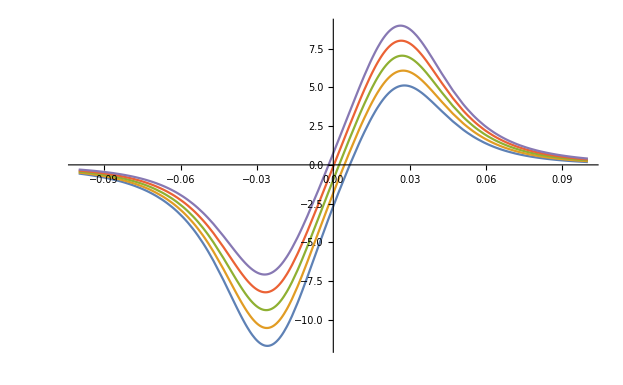

```mathematica
Plot[Evaluate@Table[AxialField[0,z,ExampleCoil[deltacur]],{deltacur, -1,1,0.5}],{z,-0.1,0.1},PlotRange->All]
```

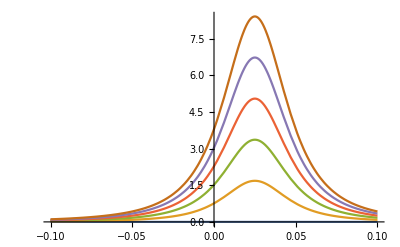

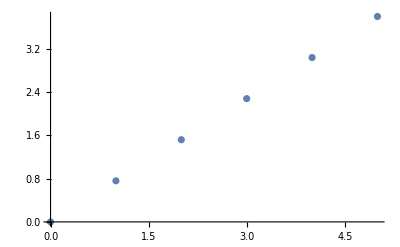

0.+0.759052 cur

```mathematica
ExampleCoil2[deltacur_] := {{0.0299,0.025,8,cur},{0.03,-0.025,10,0}};
Plot[Evaluate@Table[AxialField[0,z,ExampleCoil2[cur]],{cur, 0,5,1}],{z,-0.1,0.1},PlotRange->All]
ListPlot[Table[{cur,AxialField[0,0,ExampleCoil2[cur]]},{cur, 0,5,1}]]
AxialField[0,0,ExampleCoil2[cur]]
```

#### Generating coils lists

There are several functions to help you generate coils lists.  

The function "Helmholtz" takes  the parameters for a coil list (r, z, turns, current) and returns a coils list with two identical coils.  One has the parameters you specified, and the other has a position of -z.

The function "TrueHelmholtz" takes the same parameters except that it does not take a radius.  The radius is automatically set to 2z.

The functions "AntiHelmholtz" and "TrueAntiHelmholtz" work identically except that the mirror coil has the opposite current.

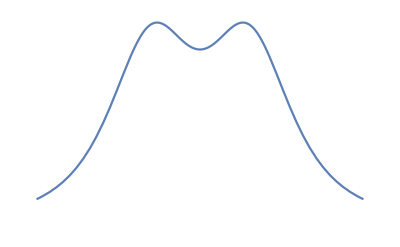

```mathematica
ExampleCoils=Helmholtz[0.4,0.3,1000,0.01];
Plot[AxialField[0,z,ExampleCoils],{z,-1,1},Axes->{False, False}]
```

There are also functions for helping generate a list of several coils with the same current or number of turns.  To use these functions, create a "precoils" list without the current or without both current and turns.

```mathematica
ExamplePreCoils={{.1,-.1}, {.1, .1}}
```

{{0.1,-0.1},{0.1,0.1}}

```mathematica
NewExamplePreCoils=WithTurns[ExamplePreCoils, 30]
```

{{0.1,-0.1,30},{0.1,0.1,30}}

```mathematica
ExampleCoils=WithCurrent[NewExamplePreCoils, .4]
```

{{0.1,-0.1,30,0.4},{0.1,0.1,30,0.4}}

Or simply

```mathematica
ExampleCoils=WithTurnsAndCurrent[ExamplePreCoils, 30, .4]
```

{{0.1,-0.1,30,0.4},{0.1,0.1,30,0.4}}

```mathematica
ExampleCoil[deltacur_] := {{0.03,0.025,10,5+deltacur},{0.03,-0.025,10,-5+deltacur}};
```

## Function Summary

coils = {{rad_1,z_1,turns_1,I_1}, {rad_2,z_2,turns_2,I_2}, ...}
coils = Helmholtz[rad, z, turns, I]
coils = TrueHelmholtz[z, turns, I]
coils = AntiHelmholtz[rad, z, turns, I]
coils = TrueAntiHelmholtz[z, turns, I]
coils = WithCurrent[precoils, I]       (where precoils is a coils list with the current missing)
precoils = WithTurns[preprecoils, turns]     (where preprecoils is a coils list with both currents and turns missing)

AxialField[r, z, coils]
RadialField[r, z, coils]
FieldMag[r, z, coils]

## LG24B Coil in Calculation

Recalling parameters of Coil of LG24B

```mathematica
z0=0.025; (*inner z offset from centre of Coil*)
dz=0.005;  (*thickness for one round*)
r0=0.052; (*inner radius of coil*)
dr=0.004;(*thickness of radius of coil*)
```

```mathematica
curr=42.77;
```

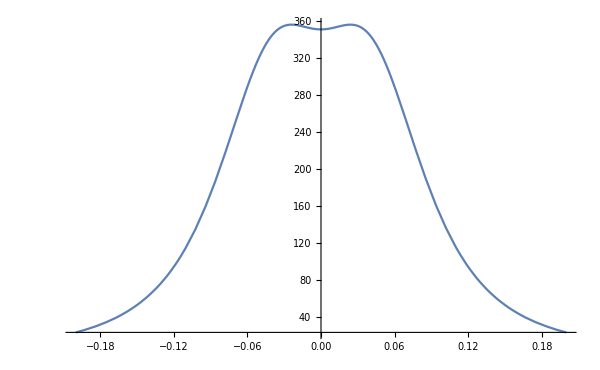

```mathematica
LG24BCoils=Flatten[Table[Helmholtz[r0+dr*n,z0+m*dz,1,curr],{n,0,9},{m,0,6}],2];
Plot[AxialField[0,z,LG24BCoils],{z,-0.2,0.2},PlotRange->All]
(*Plot[RadialField[10^-6,z,LG24BCoils],{z,0,0.001},PlotRange->All]*)
Plot[Evaluate[0.01*D[AxialField[0,z,LG24BCoils], z]],{z,0,0.0003},PlotRange->All];
```

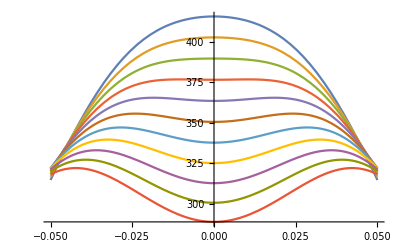

```mathematica
dz=0.005;  (*thickness for one round*)
r0=0.052; (*inner radius of coil*)
dr=0.004;(*thickness of radius of coil*)
curr=42.77;
LG24BCoils2[zv0_,z_]:=Flatten[Table[Helmholtz[r0+dr*n,zv0+m*dz,1,curr],{n,0,9},{m,0,6}],2];
Plot[Evaluate@Table[AxialField[0,z,LG24BCoils2[zv0,z]],{zv0,0.015,0.035,0.002}],{z,-0.05,0.05},PlotRange->All]
(*Plot[RadialField[10^-6,z,LG24BCoils],{z,0,0.001},PlotRange->All]*)
(*Plot[Evaluate[0.01*∂_z AxialField[0,z,LG24BCoils]],{z,0,0.0003},PlotRange->All];*)
```

We can see in calculation there is very small gradient.

However, if we check the experiment data for this gradient, we can see actually, there is large gradient here

Now, we try to use a anti-Helmholtz coil to compensate this gradient.

## Experiment data about this gradient of High Magnetic field

Even after static compensation, we still have vertical gradient larger than 0.2G/cm and horizontal gradient about 0.045G/cm.

Due to curvature, static compensation cannot satisfy our requirement. Can we have this? B-field shift with atom position?

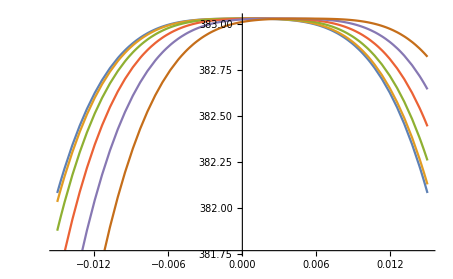

```mathematica
Plot[Evaluate@Table[AxialField[0,z-0.5*0.0001*t^2,LG24BCoils],{t,0,10,2}],{z,-0.015,0.015}]
```

## Try to compensate this gradient by Dynamic fast coil

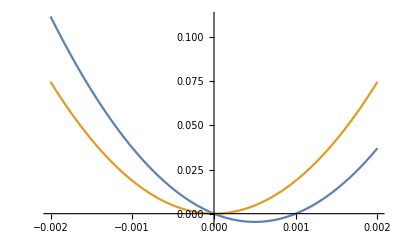

```mathematica
z0=0.025; (*inner z offset from centre of Coil*)
dz=0.005;  (*thickness for one round*)
r0=0.052; (*inner radius of coil*)
dr=0.004;(*thickness of radius of coil*)

curr=42.77;
curcom=0.2;
zt=0.002;
LG24BCoilsCom=Flatten[Table[Helmholtz[r0+dr*n,z0+m*dz,1,curr],{n,0,9},{m,0,6}],2]~Join~{{0.03,0.025,10,-curcom},{0.03,-0.025,10,curcom}};
Plot[{AxialField[0,z,LG24BCoilsCom]-350.46030481,1.869*10^4 z^2},{z,-zt,zt},PlotRange->All(*{0,All}*)(*,Axes->{False,False}*)]
(*Plot[RadialField[10^-6,z,LG24BCoilsCom],{z,0,0.0003},PlotRange->All]*)
Plot[Evaluate[0.01*D[AxialField[0,z,LG24BCoilsCom], z]],{z,-zt,zt},PlotRange->All];
```

We shift gradient zero point with atom now, however its B-field value change, so, we add current different to up and down fast coil.

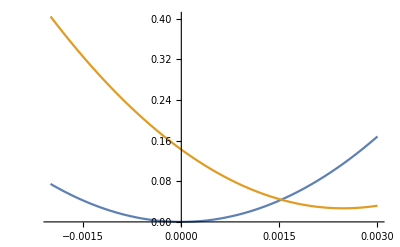

```mathematica
TotalB[z_,curcom_,delta_]:=AxialField[0,z,{{0.03,0.025,10,-curcom+delta},{0.03,-0.025,10,curcom+delta}}]+1.869*10^4 z^2;
Plot[{TotalB[z,0,0],TotalB[z,1,0.075]},{z,-0.002,0.003},PlotRange->{All,All}]
```

```mathematica
Series[TotalB[z,cur,delta],{z,0,3}]
```

1.8991 delta-93.3983 cur z+(18690.+1959.83 delta) z^2+6693.42 cur z^3+O[z]^4

Now, we take it to second order.

```mathematica
TotalB2[z_,cur_,delta_]:=1.89909901244417 delta-93.39831208741818 cur z+(18690.+1959.8334339654957 delta) z^2;
```

```mathematica
solz=Solve[D[TotalB2[z,cur,delta], z]==0,z]
solz=Solve[D[TotalB2[z,cur,0], z]==0,z]
sol=Solve[D[TotalB2[z,cur,0], z]==0,cur]
```

{{z→(46.6992 cur)/(18690.+1959.83 delta)}}

{{z→0.00249862 cur}}

{{cur→400.221 z}}

```mathematica
Solve[Evaluate[TotalB2[z,cur,delta]/.solz]==0,delta]
```

{{delta→(0.116683 cur^2)/(1.8991+0.0122354 cur^2)}}

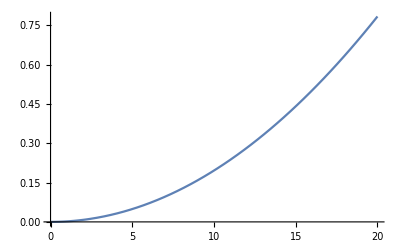

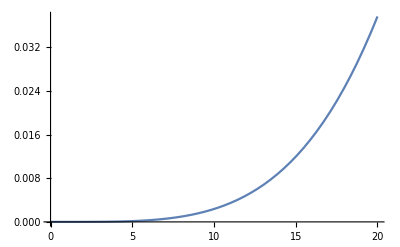

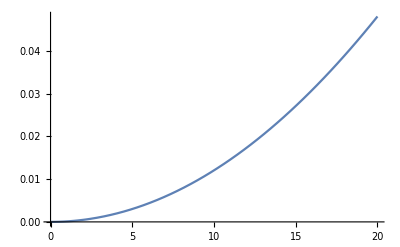

```mathematica
positionz0=0.5*9.8*t^2*10^-6;
currentcom=400.2213655104749*positionz0;
currentdelta = (0.11668331595477213 currentcom^2)/(1.89909901244417+0.012235412723066988 currentcom^2);
Plot[currentcom,{t,0,20}]
Plot[currentdelta,{t,0,20}]
Plot[currentdelta/currentcom,{t,0,20}]
```

## Solve proper coil set-up

### Theory

considering voltage-current relation of a inductance

V=L ⅆI/ⅆt

and B-field generated by a coil with N turns

B=N*μ0/2 I R^2/((R^2+z^2)^(3/2))

we have B-field controlling speed as

ⅆB/ⅆt=ⅆB/ⅆI ⅆI/ⅆt=(V N μ0)/(2L)R^2/((R^2+z^2)^(3/2))

Case#2: for single layer coil, inductance is

L=(10^-6 R^2 N^2)/(9R*0.0254+10N*2r*0.0254)∼4.374*10^-6 R N^2

where r is wire radius, if 10r still much smaller than 9R, we can discard 10r, then we have

ⅆB/ⅆt=ⅆB/ⅆI ⅆI/ⅆt=(V N μ0)/(8.749*10^-6 R N^2)R^2/((R^2+z^2)^(3/2))=0.1436*V/N R/((R^2+z^2)^(3/2))

### Coil inductance

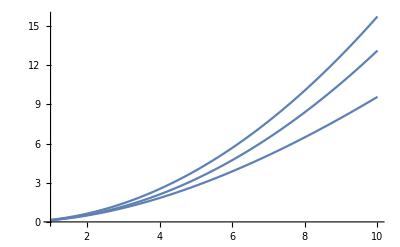

```mathematica
Lcoil={turns^2 μ0*100(Dia/2)(Log[(8Dia)/dis]-2),((Dia/2)^2 turns^2)/(9/2*Dia*0.0254+10*turns*dis*0.0254),((Dia/2)^2 turns^2)/(9/2*Dia*0.0254)};
Plot[Lcoil/.{Dia->0.06,dis->0.001},{turns,1,10}]
```

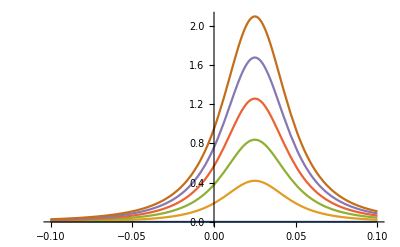

```mathematica
ExampleCoil2[cur_,turns_] := {{0.03,0.025,turns,cur},{0.03,-0.025,10,0}};
Plot[Evaluate@Table[AxialField[0,z,ExampleCoil2[cur,10]],{cur, 0,1,0.2}],{z,-0.1,0.1},PlotRange->All]
```

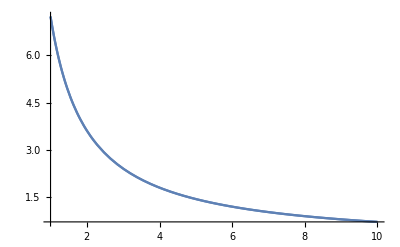

```mathematica
Plot[{10^-6 Evaluate[D[AxialField[0,0,ExampleCoil2[cur,turns]], cur]]*V/(4.374*10^-6 R turns^2),10^-2*0.1436*V/turns R/((R^2+z^2)^(3/2))}/.{V->10,R->0.03,z->0.025},{turns,1,10},PlotRange->All]
```

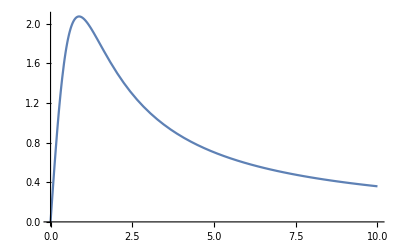

```mathematica
Plot[{10^-6 Evaluate[D[AxialField[0,0,ExampleCoil2[cur,turns]], cur]]*V/(2*4.374*10^-6 R turns^2+0.2*10^-6)}/.{V->10,R->0.03,z->0.025},{turns,0,10},PlotRange->All]
```

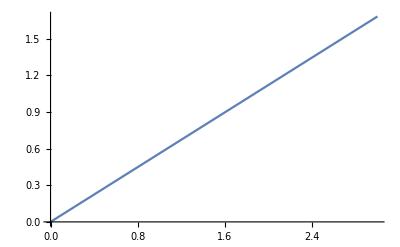

```mathematica
Plot[Evaluate[2*0.01*D[AxialField[0,z,ExampleCoil2[cu,6]], z]]/.z->0,{cu,0,3}]
```

For initial compensation, we need about 1A for 6-round coil to have the original gradient. Then, for 20ms free falling, we need compensate up to 2mm down away from optical trap center.

We need total current inside 3A.

As, two coils are connected serially, thus we have speed of magnetic field ramping about 1.2G/us when using 10V driving it.

## Calculation of coupling of coils and environment

### Simulation of coupled multi-coils with second order feedback

M_e(ⅆ I_f)/ⅆt+L_e(ⅆ I_e)/ⅆt+R_e I_e=0
M_m(ⅆ^2 I_f)/(ⅆ t^2)+L_m(ⅆ^2 I_m)/(ⅆ t^2)+R_m(ⅆ I_m)/ⅆt+1/C_m I_m=0

```mathematica
sol=DSolve[{Me*if'[t]+Le*ie'[t]+re*ie[t]==0,Mm*if''[t]+Lm*im''[t]+rm*im'[t]+cm^-1 im[t]==0,v+Lf*if'[t]==0,if[0]==0,ie[0]==0,im[0]==0},{if[t],ie[t],im[t]},t]
```

{{ie[t]→(ⅇ^(-(re t)/Le) (-1+ⅇ^((re t)/Le)) Me v)/(Lf re),if[t]→-(t v)/Lf,im[t]→-(cm^(5/2) (ⅇ^(((-cm Mm rm-√cm Mm √(-4 Lm+cm rm^2)) t)/(2 cm Lm Mm))-ⅇ^(((-cm Mm rm+√cm Mm √(-4 Lm+cm rm^2)) t)/(2 cm Lm Mm))) Lm^5 Mm C[3])/(√(-4 Lm+cm rm^2) (5 Lm^3-10 cm Lm^4+cm^2 Lm^5+3 Lm^2 rm-20 cm Lm^3 rm+5 cm^2 Lm^4 rm-15 cm Lm^2 rm^2+10 cm^2 Lm^3 rm^2-4 cm Lm rm^3+10 cm^2 Lm^2 rm^3+5 cm^2 Lm rm^4+cm^2 rm^5))}}

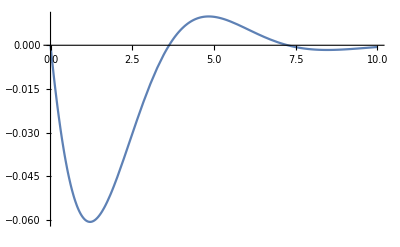

(-0.1283+0. ⅈ) ⅇ^(-0.5 t) Sin[(0.866025+0. ⅈ) t]

```mathematica
Plot[FullSimplify@N@sol[[1,3,2]]/.{re->1,Le->1,Me->1,v->1,Lf->1,cm->1,Mm->1,rm->1,Lm->1,C[3]->1},{t,0,10},PlotRange->All]
Chop@FullSimplify@N@sol[[1,3,2]]/.{re->1,Le->1,Me->1,v->1,Lf->1,cm->1,Mm->1,rm->1,Lm->1,C[3]->1}
```

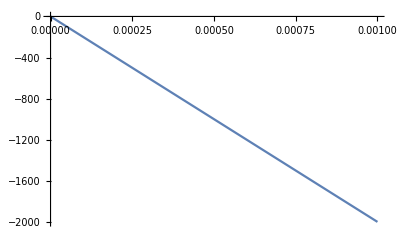

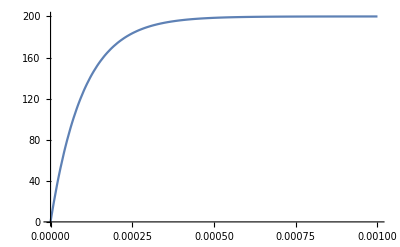

```mathematica
Plot[FullSimplify@N@sol[[1,2,2]]/.{re->0.1,Le->10^-5,Me->10^-5,v->10,Lf->5*10^-6,cm->10^-12,Mm->10^-5,rm->0.2,Lm->2*10^-3,C[3]->1},{t,0,10^-3},PlotRange->All]
Plot[FullSimplify@N@sol[[1,1,2]]/.{re->0.1,Le->10^-5,Me->10^-5,v->10,Lf->5*10^-6,cm->10^-12,Mm->10^-5,rm->0.2,Lm->2*10^-3,C[3]->1},{t,0,10^-3},PlotRange->All]
```

### A simplified case

M_e(ⅆ I_f)/ⅆt+L_e(ⅆ I_e)/ⅆt+R_e I_e=0
I_f(t)=Piecewise[{{4.5, t<0}, {2, t≥0}}]

```mathematica
sol=DSolve[{Me*if'[t]+Le*ie'[t]+re*ie[t]==0,if[t]==(4-(4-2t/τ))*HeavisideTheta[-t]+(4-2t/τ)*HeavisideTheta[-t+τ]+HeavisideTheta[t-τ]*2,ie[0]==0},{if[t],ie[t]},t]
```

{{ie[t]→-1/(Le re τ)2 ⅇ^(-(re t)/Le) (ⅇ^((re t)/Le) Me re t HeavisideTheta[-t]-Le Me HeavisideTheta[1-t] HeavisideTheta[-t]+ⅇ^((re t)/Le) Le Me HeavisideTheta[1-t] HeavisideTheta[-t]-ⅇ^((re t)/Le) Me re t HeavisideTheta[1-t] HeavisideTheta[-t]-ⅇ^(re/Le) Me re τ HeavisideTheta[1-τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-τ]+ⅇ^(re/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[1-τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[1-τ]+ⅇ^((re t)/Le) Me re τ HeavisideTheta[t-τ]-ⅇ^((re t)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[t-τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[t-τ]-ⅇ^((re t)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[1-τ] HeavisideTheta[t-τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[1-τ] HeavisideTheta[t-τ]+ⅇ^(re/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[1-τ] HeavisideTheta[t-τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[1-τ] HeavisideTheta[t-τ]+ⅇ^(re/Le) Le Me HeavisideTheta[-1+t] HeavisideTheta[-1+τ]-ⅇ^((re τ)/Le) Le Me HeavisideTheta[-1+t] HeavisideTheta[-1+τ]-ⅇ^(re/Le) Me re HeavisideTheta[-1+t] HeavisideTheta[-1+τ]+2 ⅇ^(re/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[-1+τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[-1+τ]-Me re τ HeavisideTheta[-τ]+Me re τ HeavisideTheta[1-τ] HeavisideTheta[-τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-τ] HeavisideTheta[-τ]+Le Me HeavisideTheta[τ]-ⅇ^((re τ)/Le) Le Me HeavisideTheta[τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[τ]-ⅇ^(re/Le) Le Me HeavisideTheta[-1+τ] HeavisideTheta[τ]+ⅇ^((re τ)/Le) Le Me HeavisideTheta[-1+τ] HeavisideTheta[τ]+ⅇ^(re/Le) Me re HeavisideTheta[-1+τ] HeavisideTheta[τ]-2 ⅇ^(re/Le) Me re τ HeavisideTheta[-1+τ] HeavisideTheta[τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[-1+τ] HeavisideTheta[τ]-ⅇ^((re t)/Le) Me re t HeavisideTheta[-t+τ]+2 ⅇ^((re t)/Le) Me re τ HeavisideTheta[-t+τ]-ⅇ^((re t)/Le) Le Me HeavisideTheta[1-t] HeavisideTheta[-t+τ]+ⅇ^((re τ)/Le) Le Me HeavisideTheta[1-t] HeavisideTheta[-t+τ]+ⅇ^((re t)/Le) Me re t HeavisideTheta[1-t] HeavisideTheta[-t+τ]-2 ⅇ^((re t)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[-t+τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[-t+τ]+ⅇ^(re/Le) Le Me HeavisideTheta[1-t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]-ⅇ^((re τ)/Le) Le Me HeavisideTheta[1-t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]-ⅇ^(re/Le) Me re HeavisideTheta[1-t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]+2 ⅇ^(re/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]-ⅇ^((re τ)/Le) Me re τ HeavisideTheta[1-t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]-ⅇ^((re t)/Le) Le Me HeavisideTheta[-1+t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]+ⅇ^((re τ)/Le) Le Me HeavisideTheta[-1+t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]+ⅇ^((re t)/Le) Me re t HeavisideTheta[-1+t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]-2 ⅇ^((re t)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]+ⅇ^((re τ)/Le) Me re τ HeavisideTheta[-1+t] HeavisideTheta[-1+τ] HeavisideTheta[-t+τ]),if[t]→(2 (t HeavisideTheta[-t]+τ HeavisideTheta[t-τ]-t HeavisideTheta[-t+τ]+2 τ HeavisideTheta[-t+τ]))/τ}}

```mathematica
sol[[1,1,2]]/.{re->0.001,Le->0.000001,Me->0.000001,τ->0.004,t->0.001}
```

0.31606

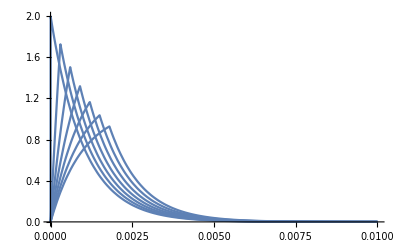

```mathematica
Plot[Table[sol[[1,1,2]]/.{re->0.001,Le->0.000001,Me->0.000001},{τ,1*10^-6,2000*10^-6,300*10^-6}],{t,0,0.01},PlotRange->All]
```